```mathematica
Plotting Basic Functions for Calculus I Ohio MOOC
```

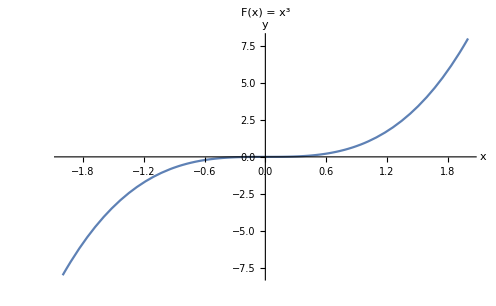

```mathematica
Plot[x^3,{x,-2, 2}, AxesLabel->{HoldForm[x],HoldForm[y]},PlotLabel->"F(x) = x^3",
LabelStyle->{FontFamily-> "Times New Roman", 12, GrayLevel[0],Bold}]
```

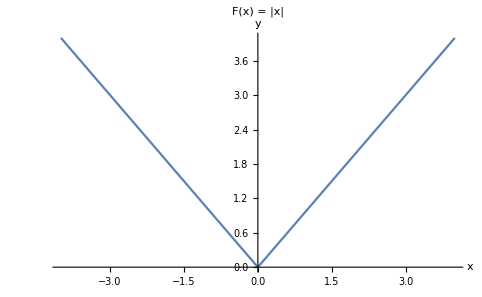

```mathematica
Plot[Abs[x],{x,-4, 4}, AxesLabel-> {HoldForm[x],HoldForm[y]},PlotLabel->"F(x) = |x|",LabelStyle->{FontFamily -> "Times New Roman", 12, GrayLevel[0], Bold}]
```

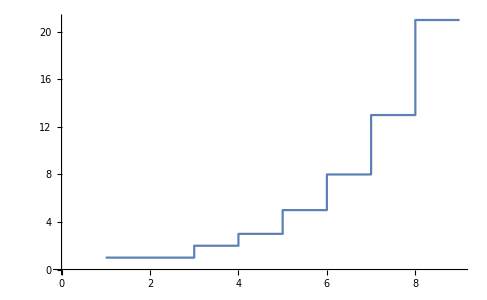

```mathematica
ListStepPlot[{1,1,2,3,5,8,13,21},Joined->True]
```

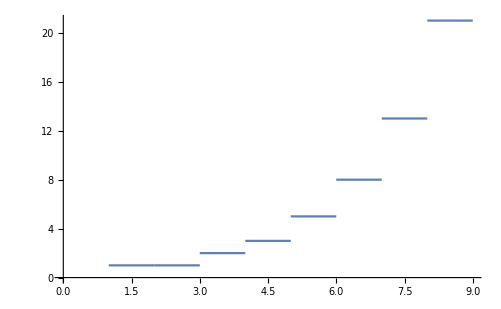

```mathematica
ListStepPlot[{1,1,2,3,5,8,13,21},Joined->False]
```

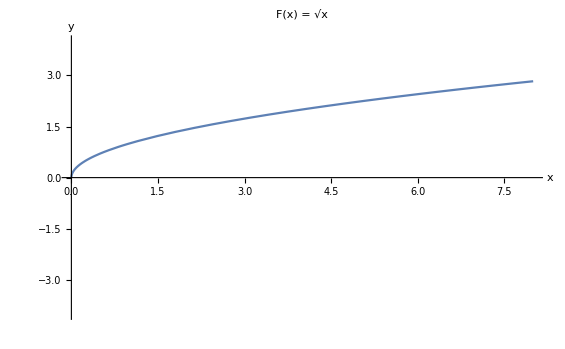

```mathematica
Plot[Sqrt[x],{x,-8, 8},PlotRange->{-4,4}, AxesLabel-> {HoldForm[x],HoldForm[y]},PlotLabel->"F(x) = √x",LabelStyle->{FontFamily -> "Times New Roman", 12, GrayLevel[0], Bold}]
```

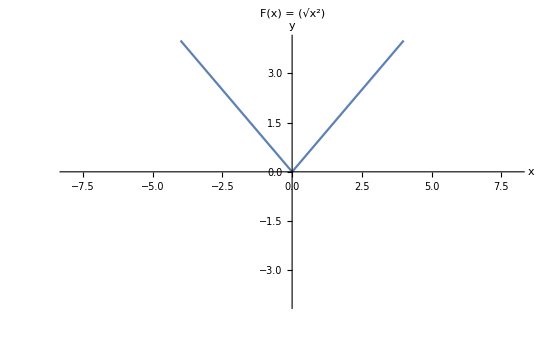

```mathematica
Plot[Sqrt[x^2],{x,-8, 8},PlotRange->{-4,4}, AxesLabel-> {HoldForm[x],HoldForm[y]},PlotLabel->"F(x) = (√(x^2))",LabelStyle->{FontFamily -> "Times New Roman", 12, GrayLevel[0], Bold}]
```

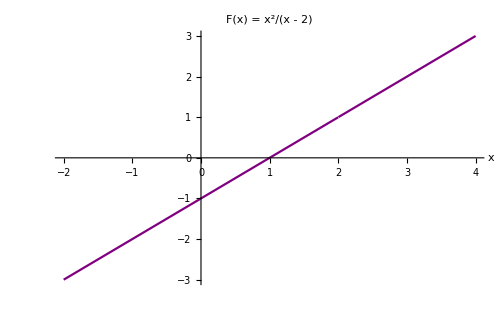

```mathematica
Plot[(x^2-3 x + 2)/(x - 2),{x,-2,4},PlotRange->{-3,3},AxesLabel->Automatic,PlotLabel-> "F(x) = x^2/(x  -  2)", LabelStyle->{FontFamily -> "Times New Roman", 12, GrayLevel[0], Bold}, PlotStyle->Purple]
```

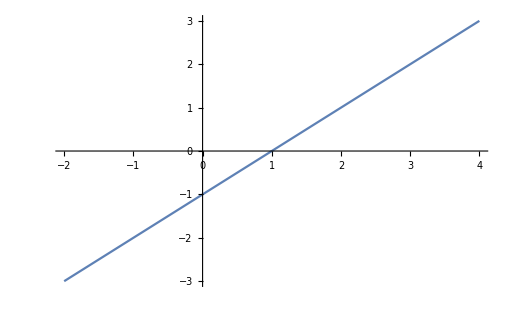

```mathematica
Plot[x-1,{x,-2,4},PlotRange->{-3,3}]
```

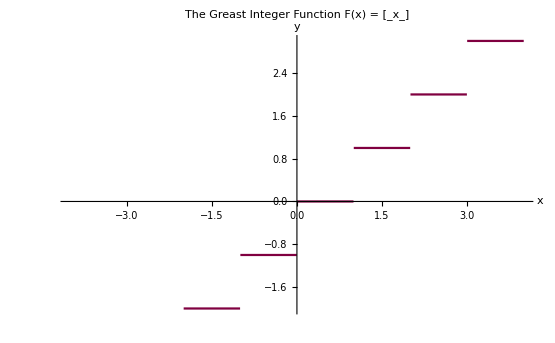

```mathematica
Plot[Floor[x],{x, -4, 4}, PlotRange->{-2,3}, AxesLabel->{HoldForm[x],HoldForm[y]},LabelStyle->{"Times New Roman",12,GrayLevel[0],Bold},PlotLabel->"The Greast Integer Function F(x) = [_x_]", PlotStyle->RGBColor[0.501961, 0, 0.25098]]
```

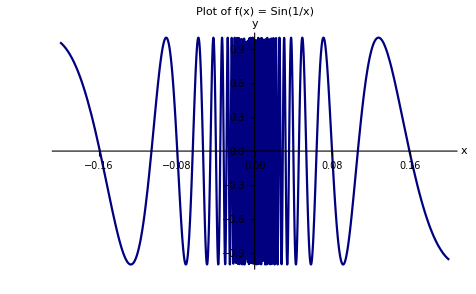

```mathematica
Plot[Sin[1/x], {x, -0.2,0.2},AxesLabel->{HoldForm[x],HoldForm[y]},LabelStyle->{"Times New Roman", 12, GrayLevel[0],Bold}, PlotLabel->"Plot of f(x) = Sin(1/x)", PlotStyle->RGBColor[0, 0, 0.501961]]
```

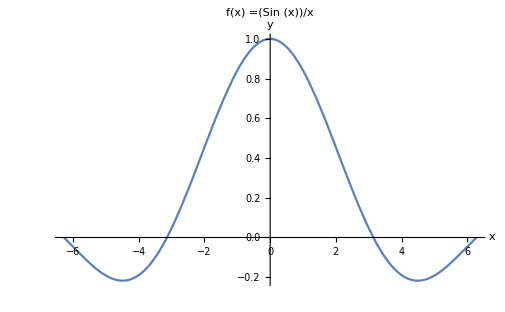

```mathematica
Plot[Sin[x]/x,{x, -2 Pi, 2 Pi}, AxesLabel->{HoldForm[x],HoldForm[y]},LabelStyle->{"Times New Roman", 12, GrayLevel[0],Bold},PlotLabel->"f(x) =(Sin (x))/x"]
```

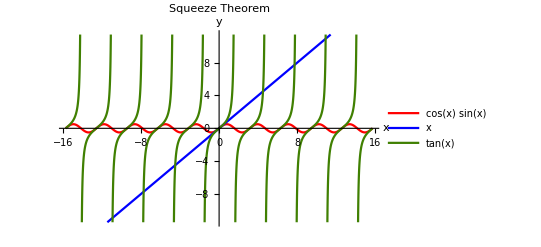

```mathematica
Plot[{Cos[x]* Sin[x] , x ,Tan[x]},{x, -5 Pi, 5 Pi}, AxesLabel->{HoldForm[x], HoldForm[y]}, LabelStyle->{"Times New Roman", 16, GrayLevel[0], Bold}, PlotStyle->{Red, Blue, RGBColor[0.25098, 0.501946, 0.00895705]}, PlotLabel->"Squeeze Theorem",PlotLegends->"Expressions"]
```

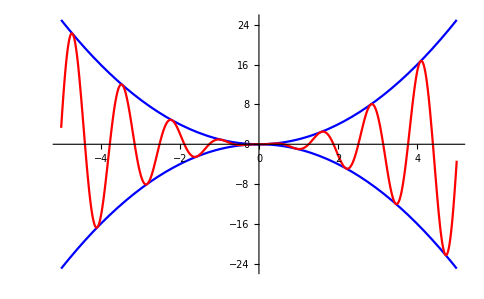

```mathematica
Plot[{x^2,-x^2,x^2 Sin[5 x]},{x,-5,5},PlotStyle->{Blue,Blue,Red}]
```

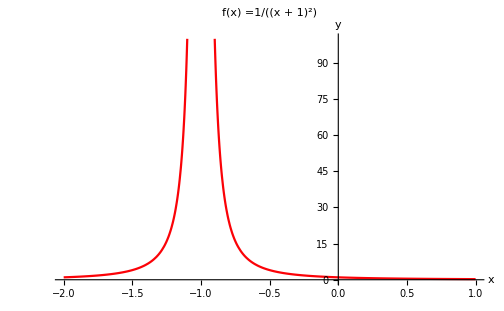

```mathematica
Plot[1/(x+1)^2,{x, -2, 1},PlotRange->{0,100}, AxesLabel->{HoldForm[x], HoldForm[y]}, LabelStyle->{"Times New Roman", 16, GrayLevel[0], Bold}, PlotStyle->RGBColor[0.986252, 0.00712596, 0.0274357], PlotLabel->"f(x) =1/(x + 1)^2",PlotLegends->"Expressions"]
```

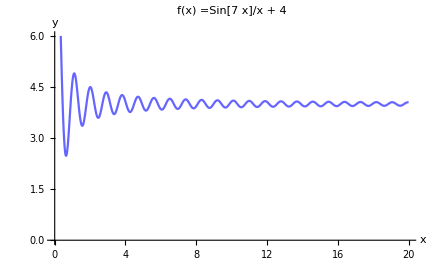

```mathematica
Plot[Sin[7  x]/x +4,{x, 0,20},PlotRange->{0,6}, AxesLabel->{HoldForm[x], HoldForm[y]}, LabelStyle->{"Times New Roman", 16, GrayLevel[0], Bold}, PlotStyle->RGBColor[0.4, 0.400107, 0.998566], PlotLabel->"f(x) =Sin[7  x]/x + 4"]
```

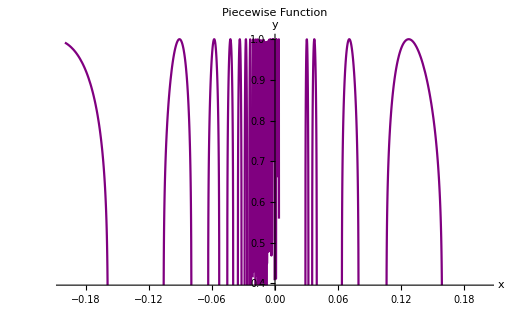

```mathematica
Plot[Piecewise[{{Sin[1/x]^(1/5),x≠0},{0 , x ==0}}],{x, -0.2, 0.2},AxesLabel -> {HoldForm[x], HoldForm[y]},PlotLabel -> "Piecewise Function", LabelStyle->{"Times New Roman", 16, GrayLevel[0],Bold},PlotStyle->RGBColor[0.501961, 0, 0.501961],PlotLegends->"Expressions"]
```

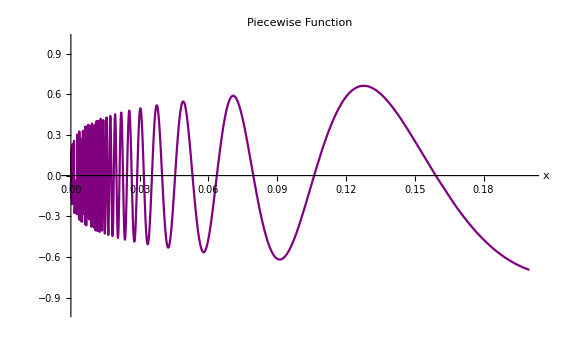

```mathematica
Plot[Piecewise[{{x^(1/5)Sin[1/x],x≠0},{0 , x ==0}}],{x, -0.2, 0.2},PlotRange->{-1,1},AxesLabel -> Automatic,PlotLabel -> "Piecewise Function", LabelStyle->{"Times New Roman", 16, GrayLevel[0],Bold},PlotStyle->RGBColor[0.501961, 0, 0.501961],PlotLegends->"Expressions"]
```